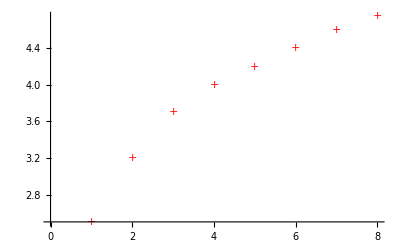

```mathematica
(*Зададим данную таблично заданную функцию*)
X={1,2,3,4,5,6,7,8};
Y={2.5,3.2,3.7,4.0,4.2,4.4,4.6,4.75};
(*Найдем количество экспериментальных точек*)
n=Dimensions[X][[1]];
(*Построим экспериментальные точки*)
XY=Table[{X[[i]],Y[[i]]},{i,1,n}];
GPoints=ListPlot[XY,PlotStyle->Red,PlotMarkers->"+"]
```

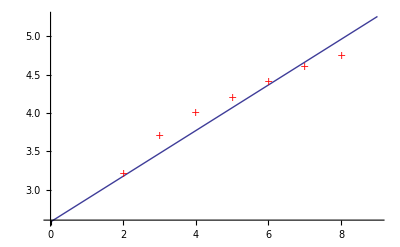

a=0.298214

b=2.57679

```mathematica
(*Зададим семейство линейных функций*)
f1[x_,a_,b_]=a*x+b;
(*Построим сумму квадратов отклонений значений семейства от экспериментальных*)
S[a_,b_]=Sum[(f1[X[[i]],a,b]-Y[[i]])^2,{i,1,n}];
(*Найдем минимум функции S*)
M1=Minimize[S[a,b],{a,b}];
(*Зададим найденную зависимость*)
y1[x_]=f1[x,a/.M1[[2,1]],b/.M1[[2,2]]];
(*Построим график найденной зависимости и экспериментальные точки в одной системе координат*)
G1=Plot[y1[x],{x,X[[1]]-1,X[[n]]+1}];
Show[G1,GPoints]
(*Найдем значение подобранных параметров*)
Print["a=",a/.M1[[2,1]]]
Print["b=",b/.M1[[2,2]]]
```

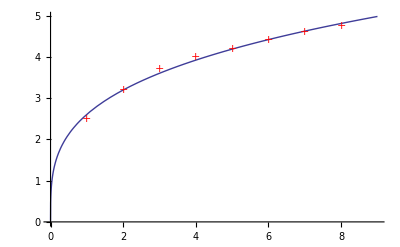

a=2.60573

b=0.294599

```mathematica
(*Зададим семейство степенных функций*)
f2[x_,a_,b_]=a*x^b;
(*Построим сумму квадратов отклонений значений семейства от экспериментальных*)
S[a_,b_]=Sum[(f2[X[[i]],a,b]-Y[[i]])^2,{i,1,n}];
(*Найдем минимум функции S*)
M2=Minimize[S[a,b],{a,b}];
(*Зададим найденную зависимость*)
y2[x_]=f2[x,a/.M2[[2,1]],b/.M2[[2,2]]];
(*Построим график найденной зависимости и экспериментальные точки в одной системе координат*)
G2=Plot[y2[x],{x,X[[1]]-1,X[[n]]+1}];
Show[G2,GPoints]
(*Найдем значение подобранных параметров*)
Print["a=",a/.M2[[2,1]]]
Print["b=",b/.M2[[2,2]]]
```

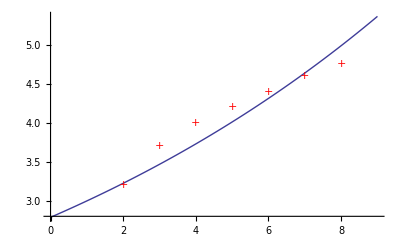

a=2.78728

b=0.0727857

```mathematica
(*Зададим семейство показательных функций*)
f3[x_,a_,b_]=a*Exp[b*x];
(*Построим сумму квадратов отклонений значений семейства от экспериментальных*)
S[a_,b_]=Sum[(f3[X[[i]],a,b]-Y[[i]])^2,{i,1,n}];
(*Найдем минимум функции S*)
M3=Minimize[S[a,b],{a,b}];
(*Зададим найденную зависимость*)
y3[x_]=f3[x,a/.M3[[2,1]],b/.M3[[2,2]]];
(*Построим график найденной зависимости и экспериментальные точки в одной системе координат*)
G3=Plot[y3[x],{x,X[[1]]-1,X[[n]]+1}];
Show[G3,GPoints]
(*Найдем значение подобранных параметров*)
Print["a=",a/.M3[[2,1]]]
Print["b=",b/.M3[[2,2]]]
```

```mathematica
(*Найдем значение отклонения для каждого семейства функций*)
Print["Отклонение для семейства линейных функций равно: ",M1[[1]]]
Print["Отклонение для семейства степенных функций равно: ",M2[[1]]]
Print["Отклонение для семейства показательных функций равно: ",M3[[1]]]
```

Отклонение для семейства линейных функций равно: 0.314554

Отклонение для семейства степенных функций равно: 0.0316595

Отклонение для семейства показательных функций равно: 0.477872

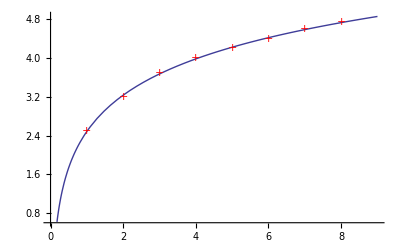

a=2.48605

b=1.08082

```mathematica
(*Зададим семейство показательных функций*)
f4[x_,a_,b_]=a+b*Log[x];
(*Построим сумму квадратов отклонений значений семейства от экспериментальных*)
S[a_,b_]=Sum[(f4[X[[i]],a,b]-Y[[i]])^2,{i,1,n}];
(*Найдем минимум функции S*)
M4=Minimize[S[a,b],{a,b}];
(*Зададим найденную зависимость*)
y4[x_]=f4[x,a/.M4[[2,1]],b/.M4[[2,2]]];
(*Построим график найденной зависимости и экспериментальные точки в одной системе координат*)
G4=Plot[y4[x],{x,X[[1]]-1,X[[n]]+1}];
Show[G4,GPoints]
(*Найдем значение подобранных параметров*)
Print["a=",a/.M4[[2,1]]]
Print["b=",b/.M4[[2,2]]]
```

```mathematica
M4[[1]]
```

0.00393514

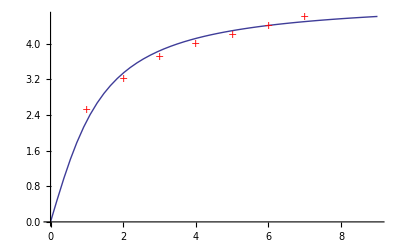

a=3.19486

b=0.860764

0.160223

```mathematica
(*Зададим семейство показательных функций*)
f5[x_,a_,b_]=a*ArcTan[b*x];
(*Построим сумму квадратов отклонений значений семейства от экспериментальных*)
S[a_,b_]=Sum[(f5[X[[i]],a,b]-Y[[i]])^2,{i,1,n}];
(*Найдем минимум функции S*)
M5=Minimize[S[a,b],{a,b}];
(*Зададим найденную зависимость*)
y5[x_]=f5[x,a/.M5[[2,1]],b/.M5[[2,2]]];
(*Построим график найденной зависимости и экспериментальные точки в одной системе координат*)
G5=Plot[y5[x],{x,X[[1]]-1,X[[n]]+1}];
Show[G5,GPoints]
(*Найдем значение подобранных параметров*)
Print["a=",a/.M5[[2,1]]]
Print["b=",b/.M5[[2,2]]]
Print[M5[[1]]]
```